Sandri Marco (2022)
LCE package for Mathematica 12
http://www.msandri.it
Email: sandri.marco@gmail.com

Marco Sandri (1996)
Numerical Calculation of Lyapunov Exponents
The Mathematica Journal, Volume 6, Issue 3, 79 - 84

Estimation of LCEs of Continuous Systems - pp. 80-81
The Lorenz model

```mathematica
JacobianMtx[funs_List,vars_List]:=Outer[D,funs,vars]

RKStep[f_,y_,y0_,dt_]:=Module[{k1,k2,k3,k4},k1=dt N[f/.Thread[y->y0]];
k2=dt N[f/.Thread[y->y0+k1/2]];
k3=dt N[f/.Thread[y->y0+k2/2]];
k4=dt N[f/.Thread[y->y0+k3]];
y0+(k1+2 k2+2 k3+k4)/6]

RKPoint[f_List,y_List,y0_List,{t1_,dt_}]:=Nest[RKStep[f,y,#,N[dt]]&,N[y0],Round[N[t1/dt]]]

RKList[f_List,y_List,y0_List,{t1_,dt_}]:=NestList[RKStep[f,y,#,N[dt]]&,N[y0],Round[N[t1/dt]]]

IntVarEq[F_List,DPhi_List,x_List,Phi_List,x0_List,Phi0_List,{t1_,dt_}]:=Module[{n,f,y,y0,yt},n=Length[x0];
f=Flatten[Join[F,DPhi]];
y=Flatten[Join[x,Phi]];
y0=Flatten[Join[x0,Phi0]];
yt=Nest[RKStep[f,y,#,N[dt]]&,N[y0],Round[N[t1/dt]]];
{First[#],Rest[#]}&@Partition[yt,n]]

F[{x_,y_,z_}]:={16(y-x),x(45.92-z)-y,x y - 4z};
x0={19,20,50};
T=20;
stepsize=0.02;
n = Length[x0];
x = Array[a,n];
Phi=Array[b,{n,n}];
DPhi=Phi.Transpose[JacobianMtx[F[x],x]];
Phi0=IdentityMatrix[n];
{xT,PhiT}=IntVarEq[F[x],DPhi,x,Phi,x0,Phi0,{T,stepsize}];
xT
PhiT // MatrixForm
u =Table[Random[],{n}];
Log[Norm[PhiT.u]]/T
```

{17.733,15.0227,53.4122}

(3.19813×10^11 | -4.95999×10^12 | 5.8275×10^12
5.44679×10^11 | -8.44743×10^12 | 9.92489×10^12
2.66765×10^11 | -4.13726×10^12 | 4.86087×10^12)

1.46757

Estimation of LCEs of Continuous Systems - pp. 81-82
The Lorenz model

```mathematica
prj[v1_,v2_]:=(v2.v1) v2/(v2.v2)
multiprj[v1_,vecs_]:=Plus@@Map[prj[v1,#]&,vecs]
GramSchm[vecs_]:=Fold[Join[#1,{#2-multiprj[#2,#1]}]&,{},vecs];

T=0.1;
PhiT =Phi0;
K=800;
s={};
Do[{xT,PhiT}=IntVarEq[F[x],DPhi,x,Phi,xT,PhiT,{T,stepsize}];
W=GramSchm[PhiT];
norms=Map[Norm,W];
s=Append[s,norms];
PhiT=W/norms,{K}];
lces=Rest[FoldList[Plus,0,Log[s]]]/(T Range[K]);
Last[lces]
```

{1.50085,0.00327127,-22.4872}

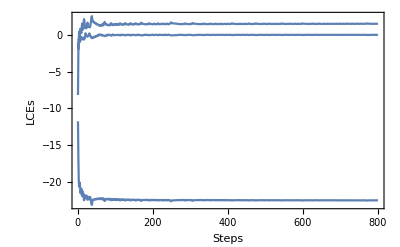

```mathematica
ConvergencePlot[x_List]:=Show[Map[ListPlot[#,Joined->True,DisplayFunction->Identity,PlotRange->All]&,Transpose[x]],Frame->True,FrameLabel->{"Steps","LCEs"},DisplayFunction->$DisplayFunction,PlotRange->All]
ConvergencePlot[lces]
```

Estimation of LCEs of Continuous Systems - pp. 81-82
The Lorenz model

```mathematica
LyapunovDimension[x_]:=Module[{l,suml,j},l=Sort[x,Greater];
suml=Rest[FoldList[Plus,0,l]];
If[Last[suml]>0,Message[LCE::pos];Return[$Failed]];
j=Last[Position[suml,_?Positive]];
First[j-suml[[j]]/l[[j+1]]]]

LCEsC[f_,initcond_,T_,K_,trans_:0,stepsize_:0.02,opts___Rule]:=Module[{opt,n,a,b,x,x0,Phi,DPhi,V0,s,W,norms,lcelist,lces},opt=LCEsPlot/.{opts}/.Options[LCEsC];
n=Length[initcond];
x=Array[a,n];
Phi=Transpose[Array[b,{n,n}]];
DPhi=Phi.Transpose[JacobianMtx[f[x],x]];
x0=Nest[RKStep[f[x],x,#,N[stepsize]]&,N[initcond],Round[N[trans/stepsize]]];
V0=IdentityMatrix[n];
s={};
Do[{x0,V0}=IntVarEq[f[x],DPhi,x,Phi,x0,V0,{T,stepsize}];
W=GramSchm[V0];
norms=Map[Norm,W];
s=Append[s,norms];
V0=W/norms,{K}];
If[opt,lcelist=Rest[FoldList[Plus,0,Log[s]]]/(T Range[K]);
Return[ConvergencePlot[lcelist]],lces=Sort[Apply[Plus,Log[s]]/(T K),Greater];
Return[{lces,LyapunovDimension[lces]}]];
]

LCEsC[F, {19, 20, 50}, 0.1, 800, 20, 0.02, LCEsPlot->False]
LCEsC[F, {19, 20, 50}, 0.1, 800, 20, 0.02, LCEsPlot->True]
```

{{1.50085,0.00327127,-22.4872},2.06689}

-Graphics-

Estimation of LCEs of Continuous Systems - p. 82
The Rössler model

```mathematica
showOrbit[sol_,patt_,f_]:=Module[{n,orbit,x,z},n=Length[First[sol]];
Which[n≥3,orbit=If[n==3&&patt=={1,2,3},sol,Map[#[[patt]]&,sol]];
Show[Graphics3D[f[orbit]],PlotRange->All,Axes->True],n==2,Show[Graphics[f[orbit]],PlotRange->All,Frame->True],n==1,x=Map[First,sol];
z=Transpose[{Drop[x,-1],Drop[x,1]}];
Show[Graphics[f[z]],PlotRange->All,Frame->True]]]

PhaseSpaceC[f_,initcond_,time_,trans_:0,stepsize_:0.02,patt_:{1,2,3}]:=Module[{n,a,x,x0,sol},n=Length[initcond];
x=Array[a,n];
x0=RKPoint[f[x],x,initcond,{trans,stepsize}];
sol=RKList[f[x],x,x0,{time,stepsize}];
showOrbit[sol,patt,Line]]

rossler[{x_,y_,z_,w_}]:=
{-y-z, x+0.25 y+w, 3 + x z, 0.05 w - 0.5 z};
x0 = {-10,-14,0.3,29};
T = 0.1; K = 2000; TR=1;  stepsize=0.02;
lcesrossler = LCEsC[rossler,x0, T, K, TR,stepsize, LCEsPlot->False]
LyapunovDimension[First[lcesrossler]]
T = 100; TR=20;
PhaseSpaceC[rossler,x0,T,TR, stepsize,{1,2,3}]
```

{{0.142461,0.00513245,-0.0040885,-24.0835},3.00596}

3.00596

-Graphics3D-

Estimation of LCEs of Continuous Systems - p. 82
The Duffing model

{{0.0791481,0.,-0.159148},2.49732}

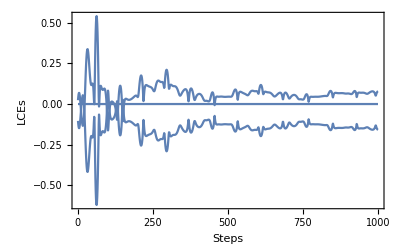

```mathematica
duffing[{x_,y_,t_}]:={y,-0.1y-x^3+10Cos[t],1}
LCEsC[duffing,{0.5,0.7,0.2},0.05,1000,10,0.02,LCEsPlot->False]
LCEsC[duffing,{0.5,0.7,0.2},0.05,1000,10,0.02,LCEsPlot->True]
```

LCEs of Discrete Systems - p..83
A four-dimensional discrete-time dynamical system

{{0.173841,0.158472,0.151448,-3.47949},3.13903}

3.13903

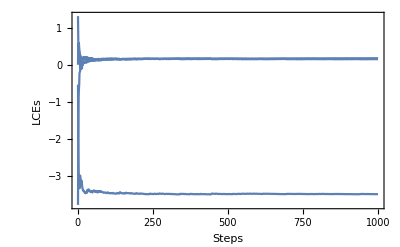

```mathematica
LCEsD[f_,initcond_,K_,trans_:0,opts___Rule]:=Module[{opt,n,a,J,s,q,r,lces},opt=LCEsPlot/.{opts}/.Options[LCEsD];
n=Length[initcond];
x=Array[a,n];
J[y_List]:=JacobianMtx[f[x],x]/.Thread[x->y];
x0=Nest[f,N[initcond],trans];
{q,r}=QRDecomposition[J[x0]];
s={};
Do[x0=f[x0];
{q,r}=QRDecomposition[J[x0].Transpose[q]];
s=Append[s,Table[r[[i,i]],{i,n}]],{K}];
If[opt,lcelist=Rest[FoldList[Plus,0,Re[Log[s]]]]/Range[K];
Return[ConvergencePlot[lcelist]],lces=Sort[Re[Apply[Plus,Log[s]]]/K,Greater];
Return[{lces,LyapunovDimension[lces]}]];
]

G[{x_,y_,z_,w_}]:={1.85-z^2 -0.05w, x, y, z}
lceshyper2 = LCEsD[G,{0.1,0,0,0}, 1000,100, LCEsPlot->False]
LyapunovDimension[First[lceshyper2]]
 LCEsD[G,{0.1,0,0,0}, 1000,100, LCEsPlot->True]
```